```mathematica
Needs["ErrorBarPlots`"]
```

## 1. Apperatefunktion

```mathematica
d0={{"λ", "U0", "Umag", "Ugelb", "Um+g", "duo", "dug"}, {400, 0.184, 0.117, 0.045, 0.041, 0.001, 0.001}, {410, 0.246, 0.150, 0.048, 0.042, 0.001, 0.001}, {420, 0.326, 0.179, 0.045, 0.041, 0.001, 0.001}, {430, 0.418, 0.201, 0.046, 0.042, 0.001, 0.001}, {440, 0.547, 0.217, 0.046, 0.042, 0.001, 0.001}, {450, 0.698, 0.218, 0.046, 0.041, 0.001, 0.001}, {460, 0.906, 0.204, 0.047, 0.041, 0.001, 0.001}, {470, 1.117, 0.163, 0.048, 0.042, 0.001, 0.001}, {480, 1.326, 0.131, 0.089, 0.046, 0.001, 0.001}, {490, 1.546, 0.098, 0.314, 0.051, 0.001, 0.001}, {500, 1.883, 0.074, 0.709, 0.053, 0.001, 0.001}, {510, 2.310, 0.064, 1.233, 0.053, 0.001, 0.001}, {520, 2.709, 0.057, 1.827, 0.052, 0.001, 0.001}, {530, 3.084, 0.051, 2.302, 0.048, 0.001, 0.001}, {540, 3.438, 0.048, 2.668, 0.047, 0.001, 0.001}, {550, 3.784, 0.049, 2.945, 0.047, 0.001, 0.001}, {560, 4.12, 0.054, 3.356, 0.051, 0.01, 0.001}, {570, 4.47, 0.054, 3.764, 0.052, 0.01, 0.001}, {580, 4.80, 0.058, 3.801, 0.054, 0.01, 0.001}, {590, 5.13, 0.088, 4.29, 0.077, 0.01, 0.01}, {600, 5.45, 0.308, 4.47, 0.237, 0.01, 0.01}};
```

## Fehler

```mathematica
dλ=0.2;
dU=0.002;(*VC230*)
```

## 2. Diode offset

```mathematica
off=0.029;
```

## 3. Farbfilter

```mathematica
d1={{"λ", "U1", "U2", "U1+2"}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}};
```

## 4. Farblösung

```mathematica
d2={{"λ", "U3"}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}};
```

```mathematica
c=1;dc=0;
```

```mathematica
x=1;dx=0;
```

## Auswertung

```mathematica
Needs["PlotLegends`"]
```

```mathematica
<<"Labor.m"
```

```mathematica
ad1=Table[Optic`Adsorbance[d0[[x,2]]-off,d0[[x,3]]-off,d0[[x,6]]*3 + d0[[x,2]]*0.008,dU*3+d0[[x,3]]*0.008],{x,2,22}];
ad2=Table[Optic`Adsorbance[d0[[x,2]]-off,d0[[x,4]]-off,d0[[x,6]]*3 + d0[[x,2]]*0.008,d0[[x,7]]]*3+d0[[x,4]]*0.008,{x,2,22}];
ad12=Table[Optic`Adsorbance[d0[[x,2]]-off,d0[[x,5]]-off,d0[[x,6]]*3 + d0[[x,2]]*0.008,dU*3+d0[[x,5]]*0.008],{x,2,22}];
add=Table[Basic`Fadd[ad1[[x,1]],ad1[[x,2]],ad2[[x,1]],ad2[[x,2]]] ,{x,1,21}];
ad1t=Table[Optic`Transmission[d0[[x,2]]-off,d0[[x,3]]-off,d0[[x,6]]*3 + d0[[x,2]]*0.008,dU*3+d0[[x,3]]*0.008],{x,2,22}];
ad2t=Table[Optic`Transmission[d0[[x,2]]-off,d0[[x,4]]-off,d0[[x,6]]*3 + d0[[x,2]]*0.008,d0[[x,7]]*3+d0[[x,4]]*0.008],{x,2,22}];
ad12t=Table[Optic`Transmission[d0[[x,2]]-off,d0[[x,5]]-off,d0[[x,6]]*3 + d0[[x,2]]*0.008,dU*3+d0[[x,5]]*0.008],{x,2,22}];
addt=Table[Basic`Fmult[ad1t[[x,1]],ad1t[[x,2]],ad2t[[x,1]],ad2t[[x,2]]] ,{x,1,21}];
```

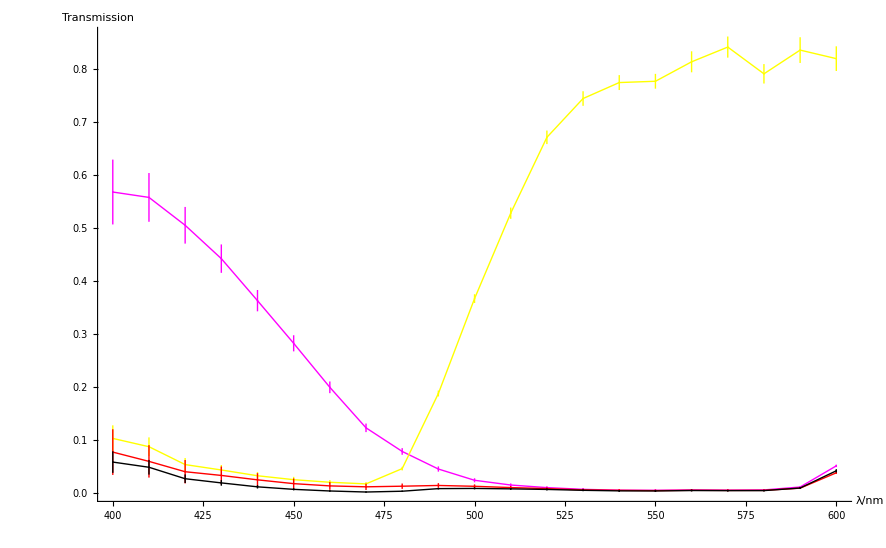

```mathematica
ErrorListPlot[{Table[{{d0[[x+1,1]],ad1t[[x,1]]},ErrorBar[dλ,ad1t[[x,2]]]},{x,1,21}],Table[{{d0[[x+1,1]],ad2t[[x,1]]},ErrorBar[dλ,ad2t[[x,2]]]},{x,1,21}],
Table[{{d0[[x+1,1]],ad12t[[x,1]]},ErrorBar[dλ,ad12t[[x,2]]]},{x,1,21}],Table[{{d0[[x+1,1]],addt[[x,1]]},ErrorBar[dλ,addt[[x,2]]]},{x,1,21}]},Joined->True,PlotStyle-> {Magenta,Yellow,Red,Black},AxesLabel->{"λ/nm","Transmission"}]
```

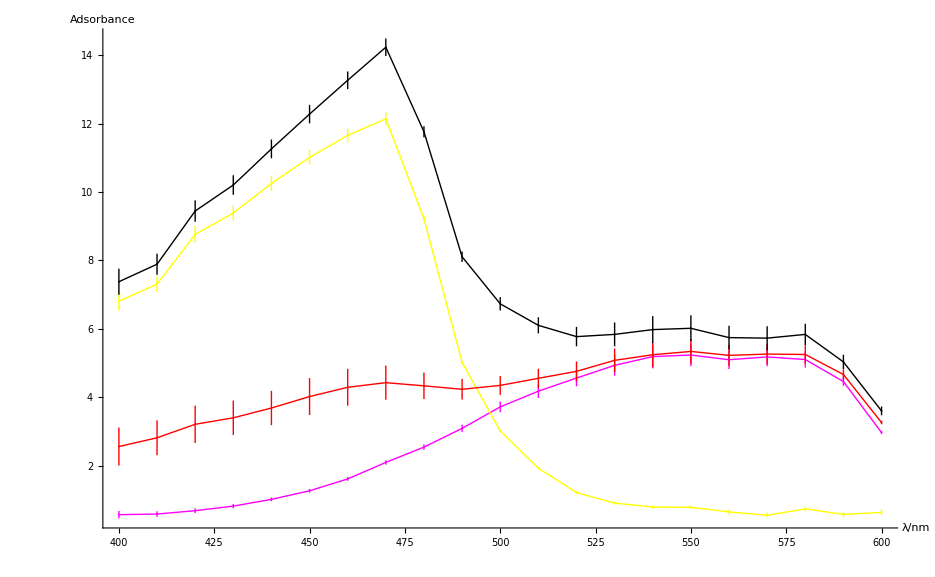

```mathematica
ErrorListPlot[{Table[{{d0[[x+1,1]],ad1[[x,1]]},ErrorBar[dλ,ad1[[x,2]]]},{x,1,21}],Table[{{d0[[x+1,1]],ad2[[x,1]]},ErrorBar[dλ,ad2[[x,2]]]},{x,1,21}],
Table[{{d0[[x+1,1]],ad12[[x,1]]},ErrorBar[dλ,ad12[[x,2]]]},{x,1,21}],Table[{{d0[[x+1,1]],add[[x,1]]},ErrorBar[dλ,add[[x,2]]]},{x,1,21}]},Joined->True,PlotStyle-> {Magenta,Yellow,Red,Black},AxesLabel->{"λ/nm","Adsorbance"}]
```

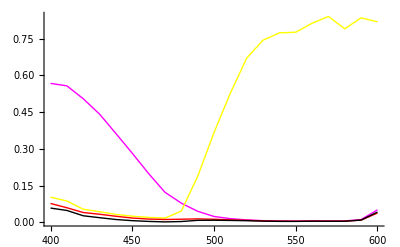

```mathematica
Show[ListPlot[{Table[{d0[[x+1,1]],ad1t[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad2t[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad12t[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad1t[[x,1]]*ad2t[[x,1]]},{x,1,21}]},PlotLegend->{"mag","yel","kombi","add"},PlotStyle-> {Magenta,Yellow,Red,Black},Joined->True]]
```